```mathematica
bigyellow = {297413941736400589979939780692294751544,4,1};
```

```mathematica
bigred = {201412842028162214137229450141139961424,4,1};
```

```mathematica
cands =DeleteDuplicates@ ;ru = cands[[13]]; ca = getca[ru, 200];
```

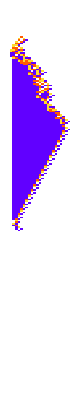
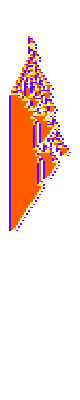
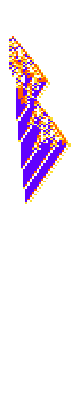
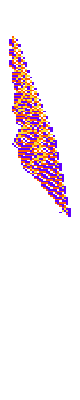
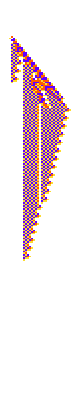
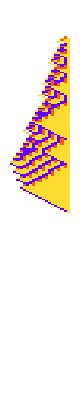
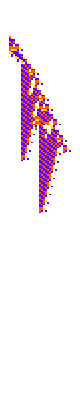
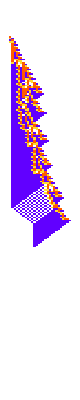

```mathematica
PlotCA/@cands
```

## Improved PerturbationSensitivities on New Rules

```mathematica
Length[quickneutral[#]]&/@Delete[cands, {{6},{16}}]
```

{16,1,1,4,1024,1024,16,1024,16,256,1,64,4,4,256,16,4,1,4,4,1,65536,4,1,1048576,1,4,1}

```mathematica
bigpop = {1, 5, 7, 9,10 ,11, 13, 17, 18, 24, 27};
```

```mathematica
PlotCA[cands[[#]]]&/@ bigpop
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

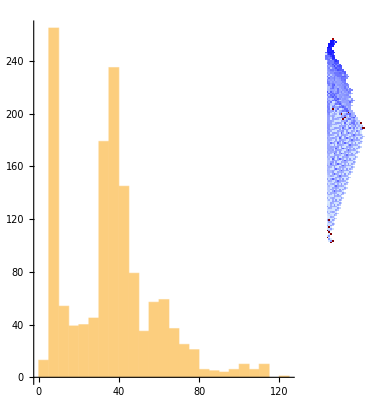

```mathematica
With[{s = PerturbationSensitivities[ru,"PerturbationFunction"->PerturbAll, "SensitivityFunction"->maxdeltalt]},GraphicsRow[{ Histogram[s, PlotRange->All],PlotSensitivities[ru, s, ImageSize->Large]}]]
```

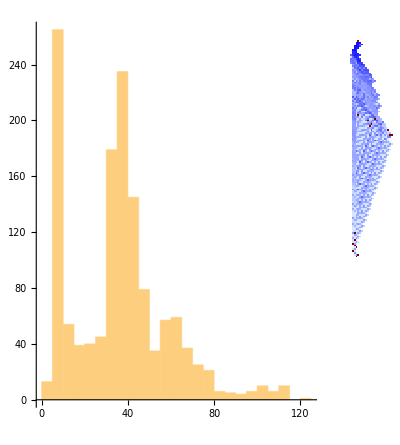
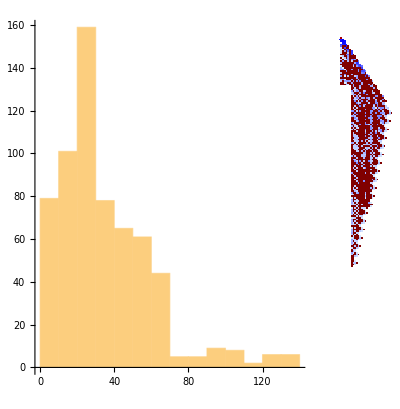
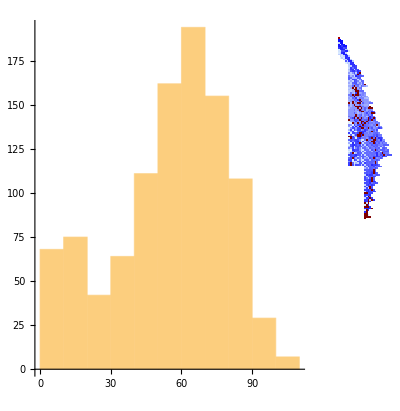
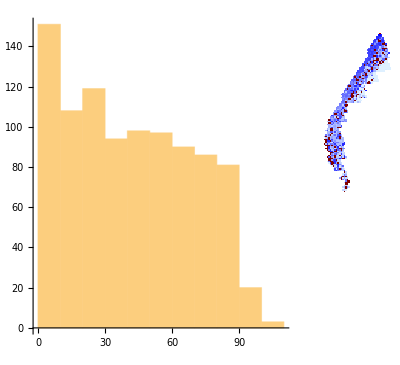
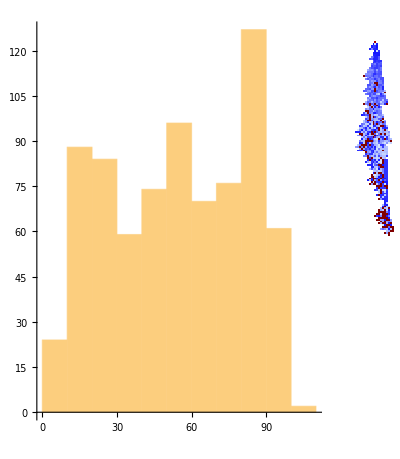
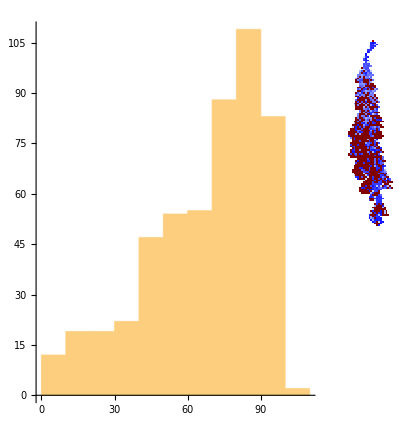
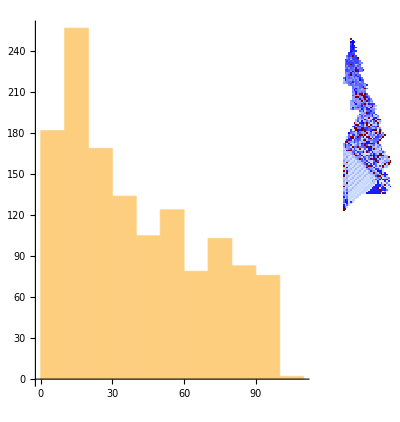
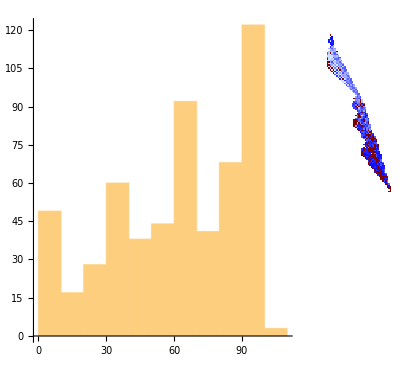

```mathematica
bps = ParallelMap[With[{s = PerturbationSensitivities[cands[[#]],"PerturbationFunction"->PerturbAll, "SensitivityFunction"->maxdeltalt]},GraphicsRow[{ Histogram[s, PlotRange->All],PlotSensitivities[cands[[#]], s, ImageSize->Large]}]]&, bigpop]
```

```mathematica
GraphicsGrid[Partition[bps, 2]]
```

-Graphics-

Big yellow

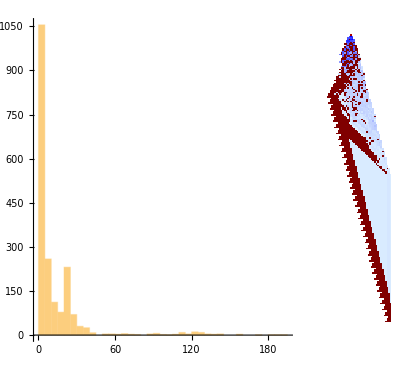

```mathematica
With[{s = PerturbationSensitivities[bigyellow,"PerturbationFunction"->PerturbAll, "SensitivityFunction"->maxdeltalt]},GraphicsRow[{ Histogram[s, PlotRange->All],PlotSensitivities[bigyellow, s, ImageSize->Large]}]]
```

Big red

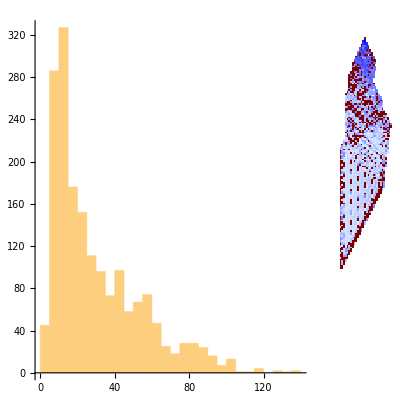

```mathematica
With[{s = PerturbationSensitivities[bigred,"PerturbationFunction"->PerturbAll, "SensitivityFunction"->maxdeltalt]},GraphicsRow[{ Histogram[s, PlotRange->All],PlotSensitivities[bigred, s, ImageSize->Large]}]]
```

## Cleaner PerturbCA

```mathematica
ru = cands[[1]];
```

```mathematica
TestLifetime[ru]
```

120

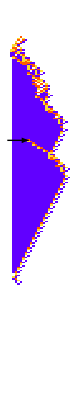

```mathematica
PerturbCA[ru] // PlotCA
```

```mathematica
PerturbCA[ru, 10]//PlotCA
```

-Graphics-

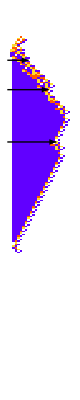

```mathematica
PerturbCA[ru, {RandomSample[#, 3]&, Last}] // PlotCA
```

```mathematica
PerturbCA[ru, 5, "BitFunction"->("SetValue"->1)] // PlotCA
```

-Graphics-

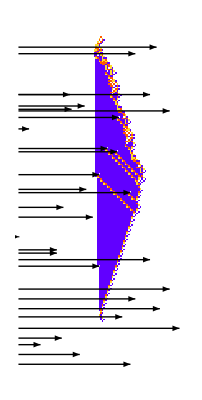

```mathematica
PerturbCA[ru,30,"Steps"->{200, {-50, 50}}, "BitFunction"->("SetValue"->0), "Body"->False] // PlotCA[#, "Trim"->{None, None}, "ArrowSize"->Medium]&
```

## Diagnosis

## Updated Cancer and Heal Functions

```mathematica
cps = getcancerperts[ru];
```

```mathematica
Length[cps]
```

156

```mathematica
perts = Select[allperts[ru],Keys[#][[1, 1]]> Keys[cps[[10]]][[1, 1]]&];
```

```mathematica
perts
```

```mathematica
healed = HealCA[ru, cps[[10]], All];
```

```mathematica
PlotCA[PerturbCA[ru, cps[[10]], "ReturnPerturbations"->True]]
```

Part::partw: Part 10 of {} does not exist.

First::nofirst: {} has zero length and no first element.

First::normal: Nonatomic expression expected at position 1 in First[10].

Part::partw: Part 1 of Integer[] does not exist.

Part::span: 1;;Integer[]⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Transpose::nmtx: The first two levels of {Integer[],{randomcomplement[#1,4]&,randomcomplement[#1,4]&}} cannot be transposed.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{{{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«3»,{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«191»}⟦1;;Integer[]⟦1,1⟧⟧,{}},evoca[{«1»},«1»]].

Transpose::perm1: Entry «1» in permutation {«1»⟦1;;Integer[]⟦1,1⟧⟧} is not a positive machine integer.

Transpose::tperm: Permutation {Integer[],{randomcomplement[#1,4]&,randomcomplement[#1,4]&}} is longer than the dimensions {0} of the expression.

AssociationMap::invrp: The argument Transpose[{},{Integer[],{randomcomplement[#1,4]&,randomcomplement[#1,4]&}}] is not a valid Association or a list.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in SparseArray[«1»].

Part::partd: Part specification «1»⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification «1»⟦-1,1⟧ is longer than depth of object.

SparseArray::list: List expected at position 1 in SparseArray[AssociationMap[{{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«3»,{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«191»}⟦#1⟦1⟧,#1⟦2⟧⟧&,«9»[«1»]]].

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::span: 1;;Integer[]⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in SparseArray[«1»].

Part::span: 1;;Integer[]⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in SparseArray[«1»].

General::stop: Further output of SparseArray::rect will be suppressed during this calculation.

Range::range: Range specification in Range[SparseArray[{{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«3»,{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«192»}][NonzeroPositions]⟦1,1⟧,«1»] does not have appropriate bounds.

$Aborted

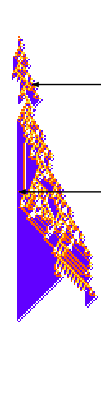
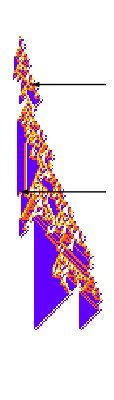
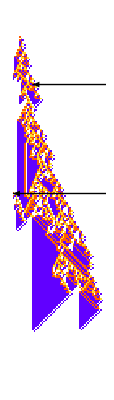
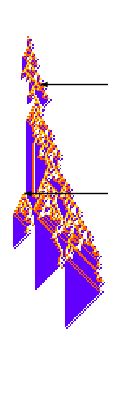
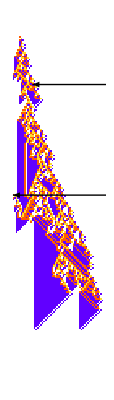
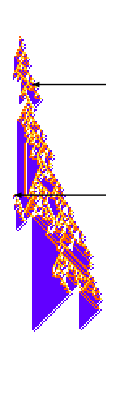
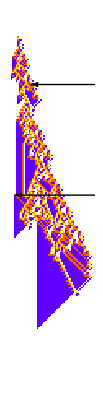
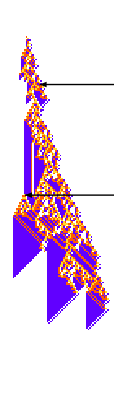

```mathematica
PlotCA/@ healed[[-10;;]]
```

```mathematica
healfunc = (#!=-Infinity&);
```

```mathematica
While[(Length[found] < max && i < Length[perts]), If[healfunc[TestCALifeTime[pca = PerturbCA[{ca, ru}, perts[[i]]]]], AppendTo[found, {pca, perts[[i]]}]]; i +=  1]
```

```mathematica
perts
```

```mathematica
perts[[1]]
```

```mathematica
found
```

0

```mathematica
Length[found]
```

0

```mathematica
max
```

1

```mathematica
i
```

1